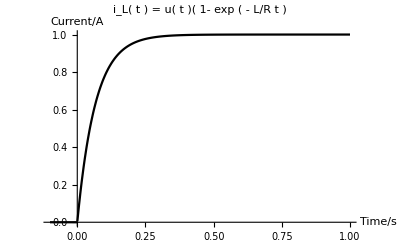

~/Desktop/Data/EE105/Homework/PS2/pic/iLt.png

0.0666667

```mathematica
L= 75*10^-6;
R = 50;
f[s_]:= (L/R)/(s^2+(L/R)*s);

p =Plot[HeavisideTheta[x]*(1-E^(-L/R*x)),{x,-1000000,10000000},PlotRange->Full,AxesLabel->{"Time/s","Current/A"}, PlotLabel->"i_L( t ) = u( t )( 1- exp ( - L/R t )",PlotTheme->"Monochrome"]
Export["~/Desktop/Data/EE105/Homework/PS2/pic/iLt.png",p]
N[1/15]
Clear["Global`*"]
```